# Delayed Rectifier

## Parameters, Equations, Differential Equations

So in the book' s description of the Hodgkin - Huxley model, it groups parameters in one cell, then all activations in the next (along with the pulse equation), and then groups the activations into the NDSolve in a third cell along with the membrane equation.The activations show up in the membrane equation.So uh, let's try that. I'll include arbitrary initial values for now, while I try to figure that stuff out.

## Parameters

```mathematica
(*parameters*)drParameters={gd->0.35,ek->-80,cn->180,vn->-25,vkn->10,sn->-17,skn->-22,cm->1700(*nf -> microFarads. This is done so that the units line up*)};
```

## Steady State Equations

```mathematica
(*equations*)
(*voltage dependence*)ninfinite[V_]=1/(1+Exp[(V-vn)/sn])/.drParameters;(*relaxation*)ka[V_]=cn/(1+Exp[(V-vkn)/skn])/.drParameters;
```

## Initial Activations/Inactivations

```mathematica
(*we must solve for the initial activation by holding at the holding voltage until the system reaches a steady state*)
initialActivation=NDSolve[{n'[t]==(ninfinite[-40]-n[t])*ka[-40],n[0]==0}/.drParameters,n[t],{t,0,100000}]
```

{{n[t]→InterpolatingFunction[…][t]}}

```mathematica
(*this gives us the initial activation value*)n[t]/.initialActivation[[1,All]]/.t->100000 (*would it be possible/useful to take a limit?*)
```

0.29269

```mathematica
ActivationSteadyState=NDSolve[{n'[t]==(ninfinite[-40]-n[t])*ka[-40],n[0]==0.29269}/.drParameters,n[t],{t,0,0.3}]
```

{{n[t]→InterpolatingFunction[…][t]}}

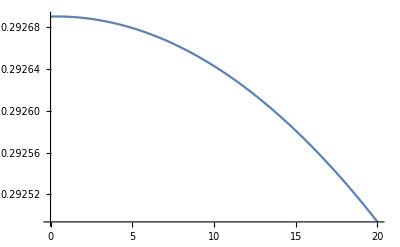

```mathematica
initActPlot=Plot[Evaluate[n[t]/.ActivationSteadyState[[1,All]]/.drParameters],{t,0,20}]
```

## Differential Equations

```mathematica
(*Differential Equations*)

{mem40,mem30,mem20,mem10,mem0,memneg10,memneg20,memneg30,memneg40,memneg50}=Table[NDSolve[{cm*V'[t]==(-(gd*(n[t])^4*(V[t]-ek))),n'[t]==(ninfinite[V[t]]-n[t])*ka[V[t]],V[0]==initV,n[0]==0.29269}/.drParameters,{V[t],n[t]},{t,0,.3}],{initV,{40,30,20,10,0,-10,-20,-30,-40,-50}}];
```

## Plots and Calculations

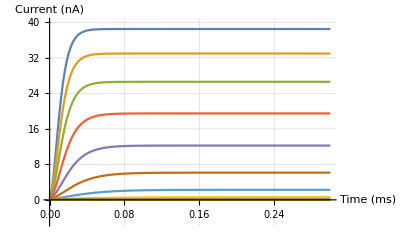

```mathematica
(*plot the current, id. I put in gd and ek values directly because replaceall is hard.*)Plot[{Evaluate[.35*n[t]^4*(V[t]+80)/.mem40[[1,All]]/.drParameters],Evaluate[.35*n[t]^4*(V[t]+80)/.mem30[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.mem20[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.mem10[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.mem0[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.memneg10[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.memneg20[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.memneg30[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.memneg40[[1,All]]/.drParameters],Evaluate[0.35*n[t]^4*(V[t]+80)/.memneg50[[1,All]]/.drParameters]},{t,0,.3},PlotRange->{{0,.3},{-5,40}},GridLines->Automatic,AxesLabel->{"Time (ms)","Current (nA)"}]
```

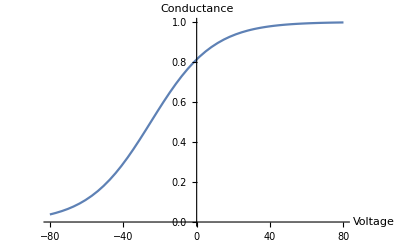

```mathematica
(*attempting to plot the voltage dependence.*)voltageDependence=Plot[1/(1+Exp[(V+25)/(-17)]),{V,-80,80},AxesLabel->{"Voltage","Conductance"}]
```

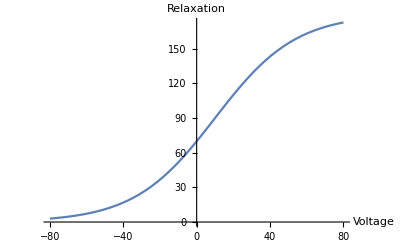

```mathematica
relaxation=Plot[cn/(1+Exp[(V-vkn)/skn])/.drParameters,{V,-80,80},AxesLabel->{"Voltage","Relaxation"}]
```

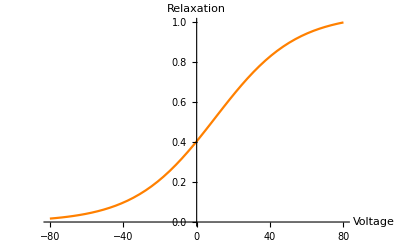

```mathematica
normRelaxation=Plot[cn/(1+Exp[(V-vkn)/skn])/ka[80]/.drParameters,{V,-80,80},AxesLabel->{"Voltage","Relaxation"},PlotStyle->Orange]
```

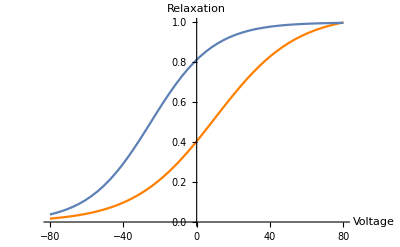

```mathematica
(*normalize the relaxation so we can overlay the plots*)
Show[normRelaxation,voltageDependence]
```